```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];

SetOptions[{Plot,ListPlot,ParametricPlot},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

# Set - Up

## Trade - Offs

```mathematica
(*Baseline transformed traits (no care)*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(*Exponential trade-off*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],r0*Exp[-c],1-(1-nu0b)*Exp[-c],1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(*Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),r0*Exp[-costR*c],1-(1-nu0b)*Exp[-costNu*c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(*Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];
```

## Base parameters

```mathematica
(* Optimal parameters*)
baseParamsEgg={ν0->0.1,σJ0->0.323823,s->6,mE->0.2,K->250,a->6};

meanEgg=0.8;
careVals=Range[0,2,0.02];
kappaVals={10,20,30};
```

## Egg death variation

```mathematica
eggMortalityDist[mean_,kappa_]:=Module[{alpha,beta},alpha=mean*kappa;
beta=(1-mean)*kappa;
BetaDistribution[alpha,beta]];
```

## Functions

```mathematica
getFitFixedC[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:fixed care c=0.5*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0.5];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*invasion Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V];

getFitAtC[params_,c_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:care=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*invasion Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V];
```

## Big Function

```mathematica
runEggMortalityCase[kappa_,n_,seed_,shape_String:"Exp"]:=Module[
{eggVals,(*sampled egg mortality values *)
paramSets,(*full parameter sets with different values*)
fitnessFixedC,(*invasion fitness at fixed care*)
resultsFixedC,(*paired (egg mortality x fitness) values*)
fitnessByCare,(*invasion fitness across care*)
meanByCare,(*mean fitness across care*)
sdByCare         (*SD of fitness across care*)},

(*fix seed*)
SeedRandom[seed];

(*draw egg mortality values*)
eggVals=RandomVariate[eggMortalityDist[meanEgg,kappa],n];

(*plot sampled egg mortality distribution*)Print[Histogram[eggVals,20,AxesLabel->{"Egg mortality (θ)","Frequency"},PlotLabel->"Egg mortality distribution ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*build full parameter sets by replacing egg death rate*)
paramSets=Table[Join[baseParamsEgg,{θ->th}],{th,eggVals}];

(*invasion fitness at fixed care c=0.5*)
fitnessFixedC=Table[getFitFixedC[paramSets[[i]],shape],{i,Length[paramSets]}];

(*pair egg mortality with fitness*)
resultsFixedC=Transpose[{eggVals,fitnessFixedC}];

(*plot fitness vs egg mortality*)Print[ListPlot[resultsFixedC,AxesLabel->{"Egg mortality (θ)","Fitness (λ)"},PlotRange->All,PlotLabel->"Fitness vs egg mortality ("<>shape<>", c = 0.5, κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*invasion fitness across care*)
fitnessByCare=Table[{c,Table[getFitAtC[paramSets[[i]],c,shape],{i,Length[paramSets]}]},{c,careVals}];

(*mean fitness across care*)
meanByCare={#[[1]],Mean[#[[2]]]}&/@fitnessByCare;

(*SD of fitness across care*)
sdByCare={#[[1]],StandardDeviation[#[[2]]]}&/@fitnessByCare;

(*plot mean fitness vs care*)Print[ListPlot[meanByCare,Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotRange->All,PlotLabel->"Mean fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*plot SD of fitness vs care*)Print[ListPlot[sdByCare,Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotRange->All,PlotLabel->"SD of fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

{meanByCare,sdByCare}];
```

# Exponential

## Bulk Code

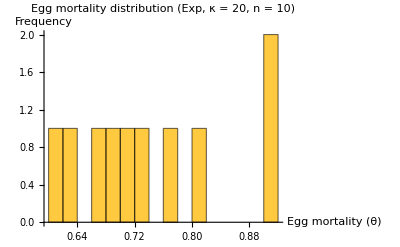

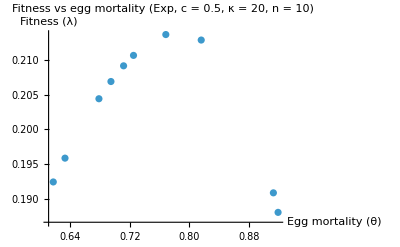

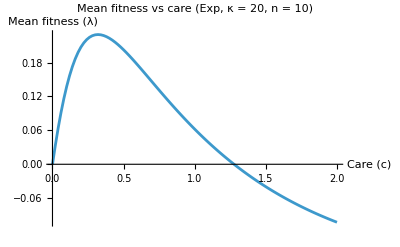

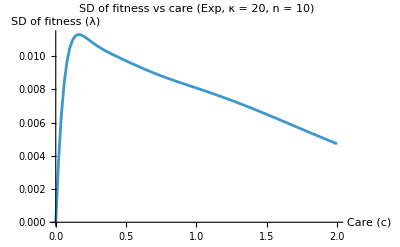

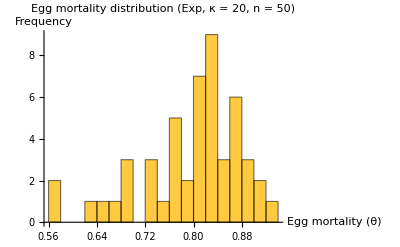

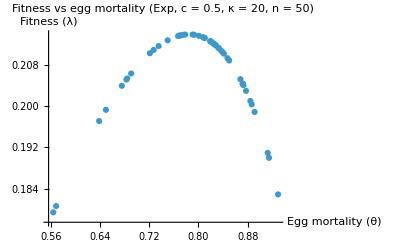

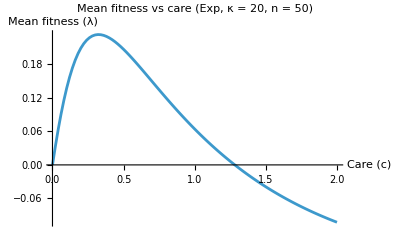

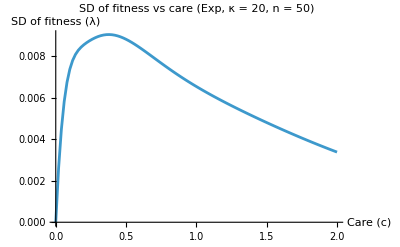

```mathematica
{meanFitnessByCareEggA10Exp,sdFitnessByCareEggA10Exp}=runEggMortalityCase[20,10,2010,"Exp"];

{meanFitnessByCareEggA50Exp,sdFitnessByCareEggA50Exp}=runEggMortalityCase[20,50,2050,"Exp"];

{meanFitnessByCareEggA100Exp,sdFitnessByCareEggA100Exp}=runEggMortalityCase[20,100,2100,"Exp"];


{meanFitnessByCareEggB10Exp,sdFitnessByCareEggB10Exp}=runEggMortalityCase[10,10,1010,"Exp"];

{meanFitnessByCareEggB50Exp,sdFitnessByCareEggB50Exp}=runEggMortalityCase[10,50,1050,"Exp"];

{meanFitnessByCareEggB100Exp,sdFitnessByCareEggB100Exp}=runEggMortalityCase[10,100,1100,"Exp"];


{meanFitnessByCareEggC10Exp,sdFitnessByCareEggC10Exp}=runEggMortalityCase[30,10,3010,"Exp"];

{meanFitnessByCareEggC50Exp,sdFitnessByCareEggC50Exp}=runEggMortalityCase[30,50,3050,"Exp"];

{meanFitnessByCareEggC100Exp,sdFitnessByCareEggC100Exp}=runEggMortalityCase[30,100,3100,"Exp"];
```

## Diagnostic Plots

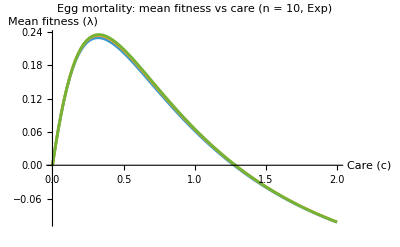

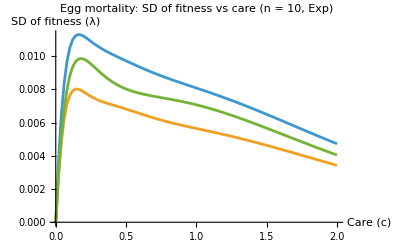

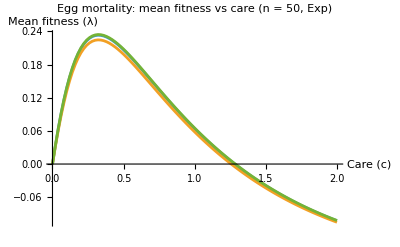

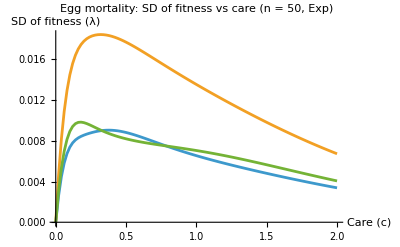

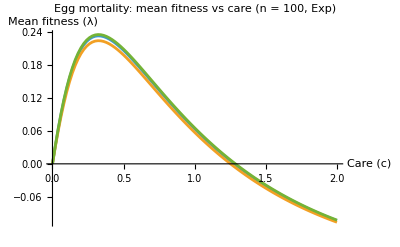

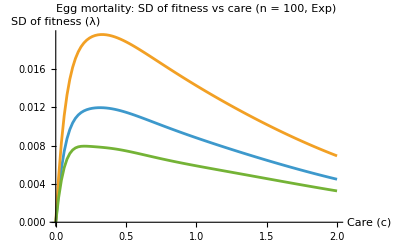

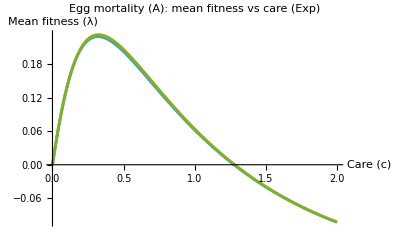

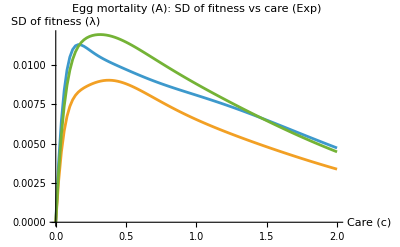

```mathematica
(*Grouped by sample size*)
ListPlot[{meanFitnessByCareEggA10Exp,meanFitnessByCareEggB10Exp,meanFitnessByCareEggC10Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: mean fitness vs care (n = 10, Exp)"]

ListPlot[{sdFitnessByCareEggA10Exp,sdFitnessByCareEggB10Exp,sdFitnessByCareEggC10Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: SD of fitness vs care (n = 10, Exp)"]


ListPlot[{meanFitnessByCareEggA50Exp,meanFitnessByCareEggB50Exp,meanFitnessByCareEggC50Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: mean fitness vs care (n = 50, Exp)"]

ListPlot[{sdFitnessByCareEggA50Exp,sdFitnessByCareEggB50Exp,sdFitnessByCareEggC50Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: SD of fitness vs care (n = 50, Exp)"]


ListPlot[{meanFitnessByCareEggA100Exp,meanFitnessByCareEggB100Exp,meanFitnessByCareEggC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: mean fitness vs care (n = 100, Exp)"]

ListPlot[{sdFitnessByCareEggA100Exp,sdFitnessByCareEggB100Exp,sdFitnessByCareEggC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Egg mortality: SD of fitness vs care (n = 100, Exp)"]

(*Grouped by distribution*)
ListPlot[{meanFitnessByCareEggA10Exp,meanFitnessByCareEggA50Exp,meanFitnessByCareEggA100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (A): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareEggA10Exp,sdFitnessByCareEggA50Exp,sdFitnessByCareEggA100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (A): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareEggB10Exp,meanFitnessByCareEggB50Exp,meanFitnessByCareEggB100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (B): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareEggB10Exp,sdFitnessByCareEggB50Exp,sdFitnessByCareEggB100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (B): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareEggC10Exp,meanFitnessByCareEggC50Exp,meanFitnessByCareEggC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (C): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareEggC10Exp,sdFitnessByCareEggC50Exp,sdFitnessByCareEggC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Egg mortality (C): SD of fitness vs care (Exp)"]
```

## Tables

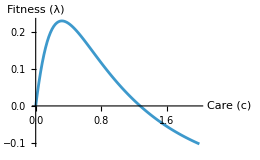
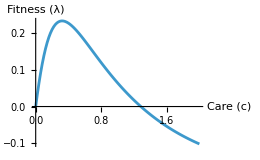
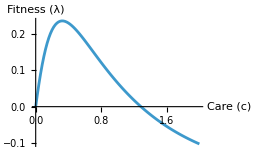
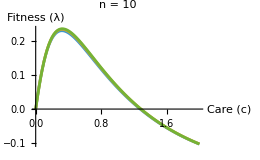
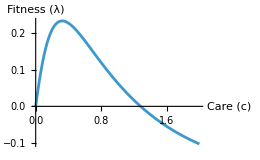
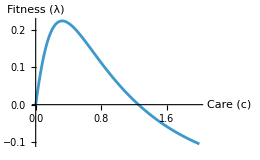
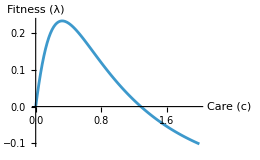
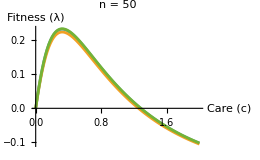
Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

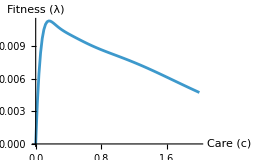
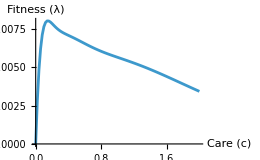
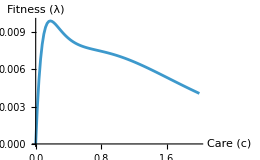
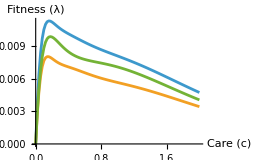
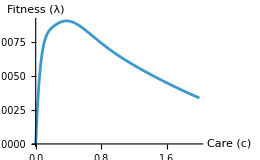
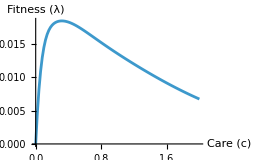
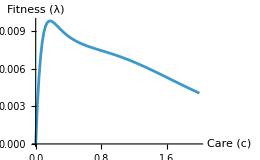
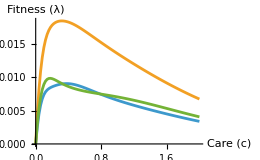
SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};

meanEggA10Exp=ListPlot[{meanFitnessByCareEggA10Exp,meanFitnessByCareEggB10Exp,meanFitnessByCareEggC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanEggA50Exp=ListPlot[{meanFitnessByCareEggA50Exp,meanFitnessByCareEggB50Exp,meanFitnessByCareEggC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanEggA100Exp=ListPlot[{meanFitnessByCareEggA100Exp,meanFitnessByCareEggB100Exp,meanFitnessByCareEggC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanEggCompAExp=ListPlot[{meanFitnessByCareEggA10Exp,meanFitnessByCareEggA50Exp,meanFitnessByCareEggA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanEggCompBExp=ListPlot[{meanFitnessByCareEggB10Exp,meanFitnessByCareEggB50Exp,meanFitnessByCareEggB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanEggCompCExp=ListPlot[{meanFitnessByCareEggC10Exp,meanFitnessByCareEggC50Exp,meanFitnessByCareEggC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableEggExp=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareEggA10Exp},plotOpts],ListPlot[{meanFitnessByCareEggB10Exp},plotOpts],ListPlot[{meanFitnessByCareEggC10Exp},plotOpts],meanEggA10Exp},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareEggA50Exp},plotOpts],ListPlot[{meanFitnessByCareEggB50Exp},plotOpts],ListPlot[{meanFitnessByCareEggC50Exp},plotOpts],meanEggA50Exp},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareEggA100Exp},plotOpts],ListPlot[{meanFitnessByCareEggB100Exp},plotOpts],ListPlot[{meanFitnessByCareEggC100Exp},plotOpts],meanEggA100Exp},{Style["Compiled",Bold],meanEggCompAExp,meanEggCompBExp,meanEggCompCExp,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableEggExp=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareEggA10Exp},plotOpts],ListPlot[{sdFitnessByCareEggB10Exp},plotOpts],ListPlot[{sdFitnessByCareEggC10Exp},plotOpts],ListPlot[{sdFitnessByCareEggA10Exp,sdFitnessByCareEggB10Exp,sdFitnessByCareEggC10Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareEggA50Exp},plotOpts],ListPlot[{sdFitnessByCareEggB50Exp},plotOpts],ListPlot[{sdFitnessByCareEggC50Exp},plotOpts],ListPlot[{sdFitnessByCareEggA50Exp,sdFitnessByCareEggB50Exp,sdFitnessByCareEggC50Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareEggA100Exp},plotOpts],ListPlot[{sdFitnessByCareEggB100Exp},plotOpts],ListPlot[{sdFitnessByCareEggC100Exp},plotOpts],ListPlot[{sdFitnessByCareEggA100Exp,sdFitnessByCareEggB100Exp,sdFitnessByCareEggC100Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareEggA10Exp,sdFitnessByCareEggA50Exp,sdFitnessByCareEggA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggB10Exp,sdFitnessByCareEggB50Exp,sdFitnessByCareEggB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggC10Exp,sdFitnessByCareEggC50Exp,sdFitnessByCareEggC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableEggExp
sdTableEggExp
```

## Big Plots

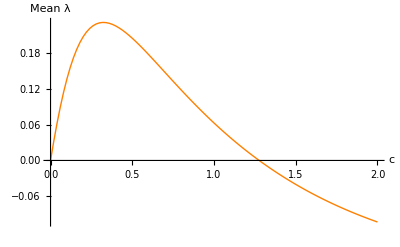

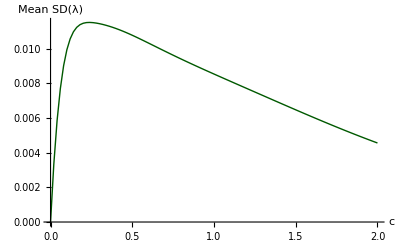

```mathematica
allMeanCurvesEggExp={meanFitnessByCareEggA10Exp,meanFitnessByCareEggA50Exp,meanFitnessByCareEggA100Exp,meanFitnessByCareEggB10Exp,meanFitnessByCareEggB50Exp,meanFitnessByCareEggB100Exp,meanFitnessByCareEggC10Exp,meanFitnessByCareEggC50Exp,meanFitnessByCareEggC100Exp};

allSDCurvesEggExp={sdFitnessByCareEggA10Exp,sdFitnessByCareEggA50Exp,sdFitnessByCareEggA100Exp,sdFitnessByCareEggB10Exp,sdFitnessByCareEggB50Exp,sdFitnessByCareEggB100Exp,sdFitnessByCareEggC10Exp,sdFitnessByCareEggC50Exp,sdFitnessByCareEggC100Exp};

careValuesEggExp=allMeanCurvesEggExp[[1]][[All,1]];

overallMeanEggExp=Transpose[{careValuesEggExp,Mean/@Transpose[allMeanCurvesEggExp[[All,All,2]]]}];

overallSDEggExp=Transpose[{careValuesEggExp,Mean/@Transpose[allSDCurvesEggExp[[All,All,2]]]}];

(*Mean*)
plotOverallMeanEggExp=ListPlot[overallMeanEggExp,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

(*SD*)
plotOverallSDEggExp=ListPlot[overallSDEggExp,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanEggExp
plotOverallSDEggExp
```

## Comparison to Deterministic

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanEggExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanEggExp];

expOneEntity=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Exponential",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

expOneEntity
```

First::nofirst: {} has zero length and no first element.

ListLinePlot::lpn: {{},{{0.,1.0003×10^-17},{0.02,0.0325269},{0.04,0.0625794},{0.06,0.0899453},{0.08,0.11453},{0.1,0.136332},{0.12,0.15542},{0.14,0.171914},{0.16,0.185962},{0.18,0.197737},{0.2,0.207415},«29»,{0.8,0.117816},{0.82,0.111996},{0.84,0.106236},{0.86,0.10054},{0.88,0.094912},{0.9,0.0893569},{0.92,0.0838771},{0.94,0.0784751},{0.96,0.0731529},{0.98,0.0679119},«51»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{First[{}],{{0.,1.0003×10^-17},{0.02,0.0325269},{0.04,0.0625794},{0.06,0.0899453},{0.08,0.11453},{0.1,0.136332},{0.12,0.15542},{0.14,0.171914},{0.16,0.185962},{0.18,0.197737},{0.2,0.207415},{0.22,0.215179},{0.24,0.221206},{0.26,0.225664},{0.28,0.228716},{0.3,0.230511},{0.32,0.231189},{0.34,0.230878},{0.36,0.229693},{0.38,0.227742},{0.4,0.225121},{0.42,0.221916},{0.44,0.218205},{0.46,0.214059},{0.48,0.209539},{0.5,0.204703},{0.52,0.1996},{0.54,0.194274},{0.56,0.188765},{0.58,0.183107},{0.6,0.177333},{0.62,0.171469},{0.64,0.165539},{0.66,0.159565},{0.68,0.153565},{0.7,0.147556},{0.72,0.141552},{0.74,0.135566},{0.76,0.129609},{0.78,0.123689},{0.8,0.117816},{0.82,0.111996},{0.84,0.106236},{0.86,0.10054},{0.88,0.094912},{0.9,0.0893569},{0.92,0.0838771},{0.94,0.0784751},{0.96,0.0731529},{0.98,0.0679119},{1.,0.0627534},{1.02,0.0576781},{1.04,0.0526867},{1.06,0.0477793},{1.08,0.042956},{1.1,0.0382168},{1.12,0.0335612},{1.14,0.0289889},{1.16,0.0244992},{1.18,0.0200915},{1.2,0.015765},{1.22,0.0115188},{1.24,0.00735202},{1.26,0.00326364},{1.28,-0.000747374},{1.3,-0.00468209},{1.32,-0.00854161},{1.34,-0.0123271},{1.36,-0.0160396},{1.38,-0.0196804},{1.4,-0.0232506},{1.42,-0.0267515},{1.44,-0.0301841},{1.46,-0.0335497},{1.48,-0.0368494},{1.5,-0.0400845},{1.52,-0.0432561},{1.54,-0.0463653},{1.56,-0.0494132},{1.58,-0.0524012},{1.6,-0.0553301},{1.62,-0.0582013},{1.64,-0.0610157},{1.66,-0.0637744},{1.68,-0.0664785},{1.7,-0.0691291},{1.72,-0.0717272},{1.74,-0.0742737},{1.76,-0.0767698},{1.78,-0.0792163},{1.8,-0.0816143},{1.82,-0.0839647},{1.84,-0.0862684},{1.86,-0.0885264},{1.88,-0.0907395},{1.9,-0.0929087},{1.92,-0.0950347},{1.94,-0.0971185},{1.96,-0.0991609},{1.98,-0.101163},{2.,-0.103125}}},PlotStyle→{Directive[First[{}],Thickness[Large]],Directive[RGBColor[1, 0.5, 0],Thickness[Large]]},PlotRange→All,AxesLabel→{c,λ},PlotLabel→Exponential
]

# Saturating

## Bulk Code

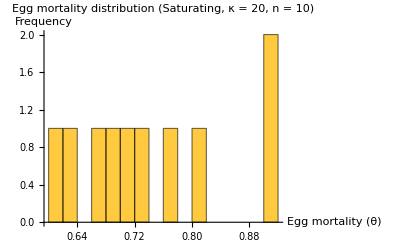

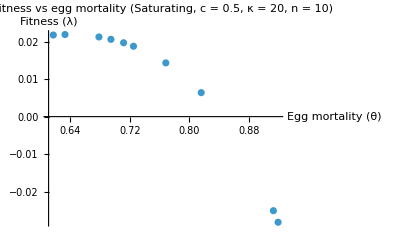

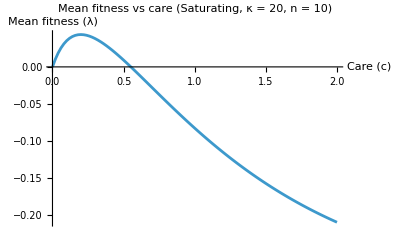

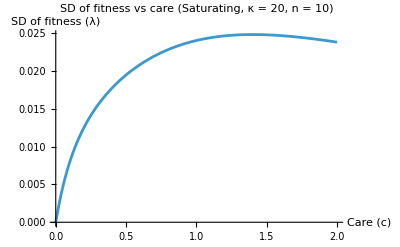

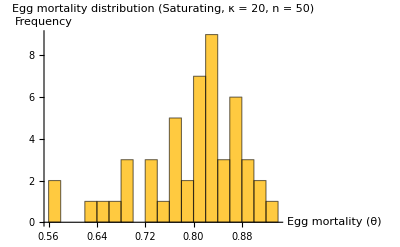

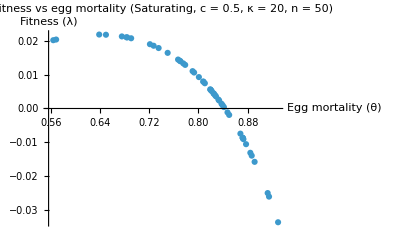

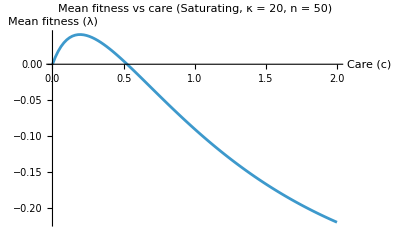

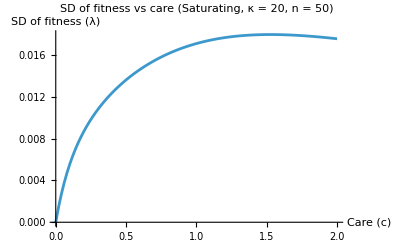

```mathematica
{meanFitnessByCareEggA10Sat,sdFitnessByCareEggA10Sat}=runEggMortalityCase[20,10,2010,"Saturating"];

{meanFitnessByCareEggA50Sat,sdFitnessByCareEggA50Sat}=runEggMortalityCase[20,50,2050,"Saturating"];

{meanFitnessByCareEggA100Sat,sdFitnessByCareEggA100Sat}=runEggMortalityCase[20,100,2100,"Saturating"];


{meanFitnessByCareEggB10Sat,sdFitnessByCareEggB10Sat}=runEggMortalityCase[10,10,1010,"Saturating"];

{meanFitnessByCareEggB50Sat,sdFitnessByCareEggB50Sat}=runEggMortalityCase[10,50,1050,"Saturating"];

{meanFitnessByCareEggB100Sat,sdFitnessByCareEggB100Sat}=runEggMortalityCase[10,100,1100,"Saturating"];


{meanFitnessByCareEggC10Sat,sdFitnessByCareEggC10Sat}=runEggMortalityCase[30,10,3010,"Saturating"];

{meanFitnessByCareEggC50Sat,sdFitnessByCareEggC50Sat}=runEggMortalityCase[30,50,3050,"Saturating"];

{meanFitnessByCareEggC100Sat,sdFitnessByCareEggC100Sat}=runEggMortalityCase[30,100,3100,"Saturating"];
```

## Diagnostic Plots

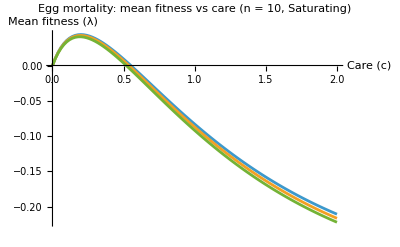

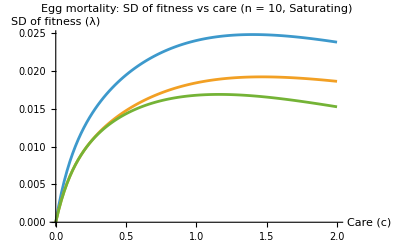

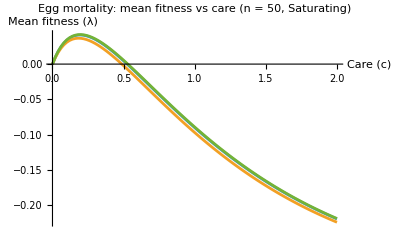

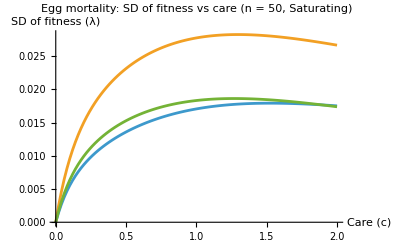

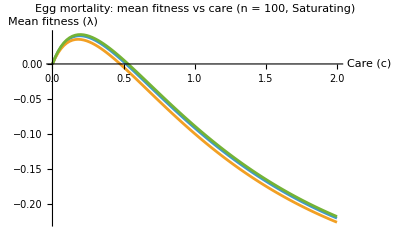

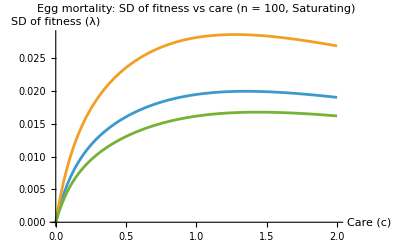

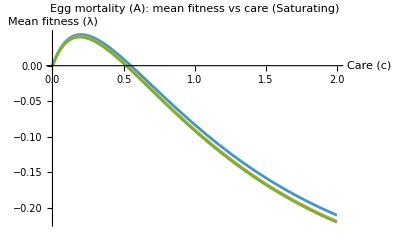

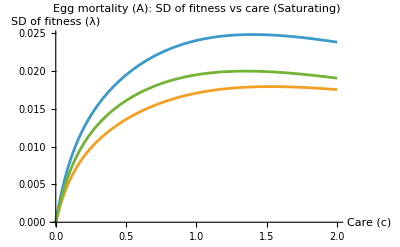

```mathematica
ListPlot[{meanFitnessByCareEggA10Sat,meanFitnessByCareEggB10Sat,meanFitnessByCareEggC10Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 10, Saturating)"]

ListPlot[{sdFitnessByCareEggA10Sat,sdFitnessByCareEggB10Sat,sdFitnessByCareEggC10Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 10, Saturating)"]


ListPlot[{meanFitnessByCareEggA50Sat,meanFitnessByCareEggB50Sat,meanFitnessByCareEggC50Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 50, Saturating)"]

ListPlot[{sdFitnessByCareEggA50Sat,sdFitnessByCareEggB50Sat,sdFitnessByCareEggC50Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 50, Saturating)"]


ListPlot[{meanFitnessByCareEggA100Sat,meanFitnessByCareEggB100Sat,meanFitnessByCareEggC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 100, Saturating)"]

ListPlot[{sdFitnessByCareEggA100Sat,sdFitnessByCareEggB100Sat,sdFitnessByCareEggC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 100, Saturating)"]



ListPlot[{meanFitnessByCareEggA10Sat,meanFitnessByCareEggA50Sat,meanFitnessByCareEggA100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (A): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareEggA10Sat,sdFitnessByCareEggA50Sat,sdFitnessByCareEggA100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (A): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareEggB10Sat,meanFitnessByCareEggB50Sat,meanFitnessByCareEggB100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (B): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareEggB10Sat,sdFitnessByCareEggB50Sat,sdFitnessByCareEggB100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (B): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareEggC10Sat,meanFitnessByCareEggC50Sat,meanFitnessByCareEggC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (C): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareEggC10Sat,sdFitnessByCareEggC50Sat,sdFitnessByCareEggC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (C): SD of fitness vs care (Saturating)"]
```

## Tables

```mathematica
meanEggA10Sat=ListPlot[{meanFitnessByCareEggA10Sat,meanFitnessByCareEggB10Sat,meanFitnessByCareEggC10Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanEggA50Sat=ListPlot[{meanFitnessByCareEggA50Sat,meanFitnessByCareEggB50Sat,meanFitnessByCareEggC50Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanEggA100Sat=ListPlot[{meanFitnessByCareEggA100Sat,meanFitnessByCareEggB100Sat,meanFitnessByCareEggC100Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanEggCompASat=ListPlot[{meanFitnessByCareEggA10Sat,meanFitnessByCareEggA50Sat,meanFitnessByCareEggA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanEggCompBSat=ListPlot[{meanFitnessByCareEggB10Sat,meanFitnessByCareEggB50Sat,meanFitnessByCareEggB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanEggCompCSat=ListPlot[{meanFitnessByCareEggC10Sat,meanFitnessByCareEggC50Sat,meanFitnessByCareEggC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];
meanTableEggSat=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareEggA10Sat},plotOpts],ListPlot[{meanFitnessByCareEggB10Sat},plotOpts],ListPlot[{meanFitnessByCareEggC10Sat},plotOpts],meanEggA10Sat},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareEggA50Sat},plotOpts],ListPlot[{meanFitnessByCareEggB50Sat},plotOpts],ListPlot[{meanFitnessByCareEggC50Sat},plotOpts],meanEggA50Sat},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareEggA100Sat},plotOpts],ListPlot[{meanFitnessByCareEggB100Sat},plotOpts],ListPlot[{meanFitnessByCareEggC100Sat},plotOpts],meanEggA100Sat},{Style["Compiled",Bold],meanEggCompASat,meanEggCompBSat,meanEggCompCSat,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
sdTableEggSat=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareEggA10Sat},plotOpts],ListPlot[{sdFitnessByCareEggB10Sat},plotOpts],ListPlot[{sdFitnessByCareEggC10Sat},plotOpts],ListPlot[{sdFitnessByCareEggA10Sat,sdFitnessByCareEggB10Sat,sdFitnessByCareEggC10Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareEggA50Sat},plotOpts],ListPlot[{sdFitnessByCareEggB50Sat},plotOpts],ListPlot[{sdFitnessByCareEggC50Sat},plotOpts],ListPlot[{sdFitnessByCareEggA50Sat,sdFitnessByCareEggB50Sat,sdFitnessByCareEggC50Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareEggA100Sat},plotOpts],ListPlot[{sdFitnessByCareEggB100Sat},plotOpts],ListPlot[{sdFitnessByCareEggC100Sat},plotOpts],ListPlot[{sdFitnessByCareEggA100Sat,sdFitnessByCareEggB100Sat,sdFitnessByCareEggC100Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareEggA10Sat,sdFitnessByCareEggA50Sat,sdFitnessByCareEggA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggB10Sat,sdFitnessByCareEggB50Sat,sdFitnessByCareEggB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggC10Sat,sdFitnessByCareEggC50Sat,sdFitnessByCareEggC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableEggSat
sdTableEggSat
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesEggSat={meanFitnessByCareEggA10Sat,meanFitnessByCareEggA50Sat,meanFitnessByCareEggA100Sat,meanFitnessByCareEggB10Sat,meanFitnessByCareEggB50Sat,meanFitnessByCareEggB100Sat,meanFitnessByCareEggC10Sat,meanFitnessByCareEggC50Sat,meanFitnessByCareEggC100Sat};
```

```mathematica
allSDCurvesEggSat={sdFitnessByCareEggA10Sat,sdFitnessByCareEggA50Sat,sdFitnessByCareEggA100Sat,sdFitnessByCareEggB10Sat,sdFitnessByCareEggB50Sat,sdFitnessByCareEggB100Sat,sdFitnessByCareEggC10Sat,sdFitnessByCareEggC50Sat,sdFitnessByCareEggC100Sat};
```

```mathematica
careValuesEggSat=allMeanCurvesEggSat[[1]][[All,1]];
```

```mathematica
overallMeanEggSat=Transpose[{careValuesEggSat,Mean/@Transpose[allMeanCurvesEggSat[[All,All,2]]]}];
```

```mathematica
overallSDEggSat=Transpose[{careValuesEggSat,Mean/@Transpose[allSDCurvesEggSat[[All,All,2]]]}];
```

```mathematica
(*Mean*)
plotOverallMeanEggSat=ListPlot[overallMeanEggSat,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];
```

```mathematica
(*SD*)
plotOverallSDEggSat=ListPlot[overallSDEggSat,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];
```

```mathematica
plotOverallMeanEggSat
```

-Graphics-

```mathematica
plotOverallSDEggSat
```

-Graphics-

## Comparison to deterministic

```mathematica
detData=getLineData[plotSaturating];
stochData=getLineData[plotOverallMeanEggSat];

detCol=getPlotColour[plotSaturating];
stochCol=getPlotColour[plotOverallMeanEggSat];

satOneEntity=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Saturating",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

satOneEntity
```

First::nofirst: {} has zero length and no first element.

ListLinePlot::lpn: {{},{{0.,1.0003×10^-17},{0.02,0.00975933},{0.04,0.0177515},{0.06,0.0242127},{0.08,0.0293454},{0.1,0.0333225},{0.12,0.0362927},{0.14,0.0383836},{0.16,0.0397053},{0.18,0.0403529},{0.2,0.040409},«30»,{0.82,-0.0578612},{0.84,-0.0616476},{0.86,-0.0654085},{0.88,-0.0691419},{0.9,-0.0728461},{0.92,-0.0765197},{0.94,-0.0801611},{0.96,-0.0837692},{0.98,-0.087343},«51»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{First[{}],{{0.,1.0003×10^-17},{0.02,0.00975933},{0.04,0.0177515},{0.06,0.0242127},{0.08,0.0293454},{0.1,0.0333225},{0.12,0.0362927},{0.14,0.0383836},{0.16,0.0397053},{0.18,0.0403529},{0.2,0.040409},{0.22,0.0399454},{0.24,0.0390248},{0.26,0.037702},{0.28,0.0360253},{0.3,0.0340369},{0.32,0.0317743},{0.34,0.0292706},{0.36,0.0265551},{0.38,0.0236538},{0.4,0.0205901},{0.42,0.0173846},{0.44,0.0140558},{0.46,0.0106204},{0.48,0.00709321},{0.5,0.00348755},{0.52,-0.000184525},{0.54,-0.00391221},{0.56,-0.00768577},{0.58,-0.0114964},{0.6,-0.0153362},{0.62,-0.0191979},{0.64,-0.0230751},{0.66,-0.0269619},{0.68,-0.030853},{0.7,-0.0347437},{0.72,-0.0386295},{0.74,-0.0425066},{0.76,-0.0463714},{0.78,-0.0502206},{0.8,-0.0540514},{0.82,-0.0578612},{0.84,-0.0616476},{0.86,-0.0654085},{0.88,-0.0691419},{0.9,-0.0728461},{0.92,-0.0765197},{0.94,-0.0801611},{0.96,-0.0837692},{0.98,-0.087343},{1.,-0.0908813},{1.02,-0.0943835},{1.04,-0.0978487},{1.06,-0.101276},{1.08,-0.104666},{1.1,-0.108017},{1.12,-0.111328},{1.14,-0.114601},{1.16,-0.117834},{1.18,-0.121027},{1.2,-0.12418},{1.22,-0.127293},{1.24,-0.130366},{1.26,-0.133398},{1.28,-0.136391},{1.3,-0.139344},{1.32,-0.142256},{1.34,-0.145129},{1.36,-0.147962},{1.38,-0.150756},{1.4,-0.153511},{1.42,-0.156226},{1.44,-0.158903},{1.46,-0.161541},{1.48,-0.16414},{1.5,-0.166702},{1.52,-0.169226},{1.54,-0.171713},{1.56,-0.174162},{1.58,-0.176575},{1.6,-0.178952},{1.62,-0.181292},{1.64,-0.183597},{1.66,-0.185867},{1.68,-0.188101},{1.7,-0.190301},{1.72,-0.192467},{1.74,-0.194599},{1.76,-0.196698},{1.78,-0.198763},{1.8,-0.200796},{1.82,-0.202797},{1.84,-0.204766},{1.86,-0.206703},{1.88,-0.208609},{1.9,-0.210485},{1.92,-0.21233},{1.94,-0.214146},{1.96,-0.215932},{1.98,-0.217688},{2.,-0.219416}}},PlotStyle→{Directive[First[{}],Thickness[Large]],Directive[RGBColor[1, 0.5, 0],Thickness[Large]]},PlotRange→All,AxesLabel→{c,λ},PlotLabel→Saturating
]

# Sigmoid

## Bulk Code

```mathematica
{meanFitnessByCareEggA10Sig,sdFitnessByCareEggA10Sig}=runEggMortalityCase[20,10,2010,"Sigmoid"];

{meanFitnessByCareEggA50Sig,sdFitnessByCareEggA50Sig}=runEggMortalityCase[20,50,2050,"Sigmoid"];

{meanFitnessByCareEggA100Sig,sdFitnessByCareEggA100Sig}=runEggMortalityCase[20,100,2100,"Sigmoid"];


{meanFitnessByCareEggB10Sig,sdFitnessByCareEggB10Sig}=runEggMortalityCase[10,10,1010,"Sigmoid"];

{meanFitnessByCareEggB50Sig,sdFitnessByCareEggB50Sig}=runEggMortalityCase[10,50,1050,"Sigmoid"];

{meanFitnessByCareEggB100Sig,sdFitnessByCareEggB100Sig}=runEggMortalityCase[10,100,1100,"Sigmoid"];


{meanFitnessByCareEggC10Sig,sdFitnessByCareEggC10Sig}=runEggMortalityCase[30,10,3010,"Sigmoid"];

{meanFitnessByCareEggC50Sig,sdFitnessByCareEggC50Sig}=runEggMortalityCase[30,50,3050,"Sigmoid"];

{meanFitnessByCareEggC100Sig,sdFitnessByCareEggC100Sig}=runEggMortalityCase[30,100,3100,"Sigmoid"];
```

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## Diagnostic Plots

```mathematica
ListPlot[{meanFitnessByCareEggA10Sig,meanFitnessByCareEggB10Sig,meanFitnessByCareEggC10Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 10, Sigmoid)"]

ListPlot[{sdFitnessByCareEggA10Sig,sdFitnessByCareEggB10Sig,sdFitnessByCareEggC10Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 10, Sigmoid)"]


ListPlot[{meanFitnessByCareEggA50Sig,meanFitnessByCareEggB50Sig,meanFitnessByCareEggC50Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 50, Sigmoid)"]

ListPlot[{sdFitnessByCareEggA50Sig,sdFitnessByCareEggB50Sig,sdFitnessByCareEggC50Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 50, Sigmoid)"]


ListPlot[{meanFitnessByCareEggA100Sig,meanFitnessByCareEggB100Sig,meanFitnessByCareEggC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: mean fitness vs care (n = 100, Sigmoid)"]

ListPlot[{sdFitnessByCareEggA100Sig,sdFitnessByCareEggB100Sig,sdFitnessByCareEggC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Egg mortality: SD of fitness vs care (n = 100, Sigmoid)"]


ListPlot[{meanFitnessByCareEggA10Sig,meanFitnessByCareEggA50Sig,meanFitnessByCareEggA100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (A): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareEggA10Sig,sdFitnessByCareEggA50Sig,sdFitnessByCareEggA100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (A): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareEggB10Sig,meanFitnessByCareEggB50Sig,meanFitnessByCareEggB100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (B): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareEggB10Sig,sdFitnessByCareEggB50Sig,sdFitnessByCareEggB100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (B): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareEggC10Sig,meanFitnessByCareEggC50Sig,meanFitnessByCareEggC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (C): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareEggC10Sig,sdFitnessByCareEggC50Sig,sdFitnessByCareEggC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Egg mortality (C): SD of fitness vs care (Sigmoid)"]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## Tables

```mathematica
meanEggA10Sig=ListPlot[{meanFitnessByCareEggA10Sig,meanFitnessByCareEggB10Sig,meanFitnessByCareEggC10Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanEggA50Sig=ListPlot[{meanFitnessByCareEggA50Sig,meanFitnessByCareEggB50Sig,meanFitnessByCareEggC50Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanEggA100Sig=ListPlot[{meanFitnessByCareEggA100Sig,meanFitnessByCareEggB100Sig,meanFitnessByCareEggC100Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanEggCompASig=ListPlot[{meanFitnessByCareEggA10Sig,meanFitnessByCareEggA50Sig,meanFitnessByCareEggA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanEggCompBSig=ListPlot[{meanFitnessByCareEggB10Sig,meanFitnessByCareEggB50Sig,meanFitnessByCareEggB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanEggCompCSig=ListPlot[{meanFitnessByCareEggC10Sig,meanFitnessByCareEggC50Sig,meanFitnessByCareEggC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableEggSig=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareEggA10Sig},plotOpts],ListPlot[{meanFitnessByCareEggB10Sig},plotOpts],ListPlot[{meanFitnessByCareEggC10Sig},plotOpts],meanEggA10Sig},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareEggA50Sig},plotOpts],ListPlot[{meanFitnessByCareEggB50Sig},plotOpts],ListPlot[{meanFitnessByCareEggC50Sig},plotOpts],meanEggA50Sig},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareEggA100Sig},plotOpts],ListPlot[{meanFitnessByCareEggB100Sig},plotOpts],ListPlot[{meanFitnessByCareEggC100Sig},plotOpts],meanEggA100Sig},{Style["Compiled",Bold],meanEggCompASig,meanEggCompBSig,meanEggCompCSig,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
sdTableEggSig=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareEggA10Sig},plotOpts],ListPlot[{sdFitnessByCareEggB10Sig},plotOpts],ListPlot[{sdFitnessByCareEggC10Sig},plotOpts],ListPlot[{sdFitnessByCareEggA10Sig,sdFitnessByCareEggB10Sig,sdFitnessByCareEggC10Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareEggA50Sig},plotOpts],ListPlot[{sdFitnessByCareEggB50Sig},plotOpts],ListPlot[{sdFitnessByCareEggC50Sig},plotOpts],ListPlot[{sdFitnessByCareEggA50Sig,sdFitnessByCareEggB50Sig,sdFitnessByCareEggC50Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareEggA100Sig},plotOpts],ListPlot[{sdFitnessByCareEggB100Sig},plotOpts],ListPlot[{sdFitnessByCareEggC100Sig},plotOpts],ListPlot[{sdFitnessByCareEggA100Sig,sdFitnessByCareEggB100Sig,sdFitnessByCareEggC100Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareEggA10Sig,sdFitnessByCareEggA50Sig,sdFitnessByCareEggA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggB10Sig,sdFitnessByCareEggB50Sig,sdFitnessByCareEggB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareEggC10Sig,sdFitnessByCareEggC50Sig,sdFitnessByCareEggC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
meanTableEggSig
sdTableEggSig
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesEggSig={meanFitnessByCareEggA10Sig,meanFitnessByCareEggA50Sig,meanFitnessByCareEggA100Sig,meanFitnessByCareEggB10Sig,meanFitnessByCareEggB50Sig,meanFitnessByCareEggB100Sig,meanFitnessByCareEggC10Sig,meanFitnessByCareEggC50Sig,meanFitnessByCareEggC100Sig};

allSDCurvesEggSig={sdFitnessByCareEggA10Sig,sdFitnessByCareEggA50Sig,sdFitnessByCareEggA100Sig,sdFitnessByCareEggB10Sig,sdFitnessByCareEggB50Sig,sdFitnessByCareEggB100Sig,sdFitnessByCareEggC10Sig,sdFitnessByCareEggC50Sig,sdFitnessByCareEggC100Sig};

careValuesEggSig=allMeanCurvesEggSig[[1]][[All,1]];

overallMeanEggSig=Transpose[{careValuesEggSig,Mean/@Transpose[allMeanCurvesEggSig[[All,All,2]]]}];

overallSDEggSig=Transpose[{careValuesEggSig,Mean/@Transpose[allSDCurvesEggSig[[All,All,2]]]}];

(*Mean*)
plotOverallMeanEggSig=ListPlot[overallMeanEggSig,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

(*SD*)
plotOverallSDEggSig=ListPlot[overallSDEggSig,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanEggSig
plotOverallSDEggSig
```

-Graphics-

-Graphics-

## Comparison to Deterministic

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

detData=getLineData[plotSigmoid];
stochData=getLineData[plotOverallMeanEggSig];

detCol=getPlotColour[plotSigmoid];
stochCol=getPlotColour[plotOverallMeanEggSig];

sigmoidOneEntity=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->All,AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Sigmoid",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

sigmoidOneEntity
```

First::nofirst: {} has zero length and no first element.

ListLinePlot::lpn: {{},{{0.,5.04537×10^-18},{0.02,-0.0112736},{0.04,-0.0214089},{0.06,-0.0302594},{0.08,-0.0376608},{0.1,-0.0434332},{0.12,-0.0473859},{0.14,-0.0493256},{0.16,-0.0490687},{0.18,-0.0464586},{0.2,-0.0413874},«30»,{0.82,0.104593},{0.84,0.099079},{0.86,0.0935691},{0.88,0.088082},{0.9,0.0826329},{0.92,0.0772339},{0.94,0.0718947},{0.96,0.0666229},{0.98,0.0614243},«51»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{First[{}],{{0.,5.04537×10^-18},{0.02,-0.0112736},{0.04,-0.0214089},{0.06,-0.0302594},{0.08,-0.0376608},{0.1,-0.0434332},{0.12,-0.0473859},{0.14,-0.0493256},{0.16,-0.0490687},{0.18,-0.0464586},{0.2,-0.0413874},{0.22,-0.0338199},{0.24,-0.0238193},{0.26,-0.0115665},{0.28,0.0026297},{0.3,0.0183384},{0.32,0.0350304},{0.34,0.0521184},{0.36,0.0690063},{0.38,0.0851404},{0.4,0.100051},{0.42,0.113381},{0.44,0.124894},{0.46,0.134474},{0.48,0.142104},{0.5,0.147849},{0.52,0.151832},{0.54,0.154213},{0.56,0.155168},{0.58,0.154881},{0.6,0.153527},{0.62,0.151274},{0.64,0.14827},{0.66,0.144652},{0.68,0.140535},{0.7,0.136021},{0.72,0.131197},{0.74,0.126135},{0.76,0.120897},{0.78,0.115533},{0.8,0.110087},{0.82,0.104593},{0.84,0.099079},{0.86,0.0935691},{0.88,0.088082},{0.9,0.0826329},{0.92,0.0772339},{0.94,0.0718947},{0.96,0.0666229},{0.98,0.0614243},{1.,0.0563035},{1.02,0.0512636},{1.04,0.0463072},{1.06,0.0414358},{1.08,0.0366503},{1.1,0.0319514},{1.12,0.027339},{1.14,0.0228129},{1.16,0.0183726},{1.18,0.0140173},{1.2,0.00974623},{1.22,0.00555823},{1.24,0.00145221},{1.26,-0.00257303},{1.28,-0.00651877},{1.3,-0.0103863},{1.32,-0.014177},{1.34,-0.0178922},{1.36,-0.0215332},{1.38,-0.0251015},{1.4,-0.0285983},{1.42,-0.0320252},{1.44,-0.0353833},{1.46,-0.038674},{1.48,-0.0418988},{1.5,-0.0450587},{1.52,-0.0481553},{1.54,-0.0511896},{1.56,-0.0541629},{1.58,-0.0570765},{1.6,-0.0599316},{1.62,-0.0627293},{1.64,-0.0654708},{1.66,-0.0681572},{1.68,-0.0707897},{1.7,-0.0733692},{1.72,-0.075897},{1.74,-0.078374},{1.76,-0.0808012},{1.78,-0.0831798},{1.8,-0.0855105},{1.82,-0.0877945},{1.84,-0.0900327},{1.86,-0.092226},{1.88,-0.0943753},{1.9,-0.0964814},{1.92,-0.0985453},{1.94,-0.100568},{1.96,-0.10255},{1.98,-0.104492},{2.,-0.106396}}},PlotStyle→{Directive[First[{}],Thickness[Large]],Directive[RGBColor[1, 0.5, 0],Thickness[Large]]},PlotRange→All,AxesLabel→{c,λ},PlotLabel→Sigmoid
]

# Deterministic Shape

```mathematica
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));


(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[
{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

params1={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};
params2={θ->0.7999967491603689,ν0->0.10000440803427434,σJ0->0.32383733876731385,s->5.999984154933559,mE->0.19999923208705223,K->250,a->6};
params3={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};

fit1=getFit[params1,"Exp"];
fit2=getFit[params2,"Saturating"];
fit3=getFit[params3,"Sigmoid"];

plotExp=ListPlot[fit1,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSaturating=ListPlot[fit2,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSigmoid=ListPlot[fit3,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];

plotExp
plotSaturating
plotSigmoid
```

-Graphics-

-Graphics-

-Graphics-

# SD Trend

```mathematica
imgW=520;
imgH=300;

meanStyle=Directive[Orange,Thick];
sdStyle=Directive[RGBColor[0,0.35,0],Thick];

extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];

makeMeanSDOverlayFromPlots[meanG_,sdG_,title_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight},meanData=extractXY[meanG];
sdData=extractXY[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
(*SD cannot be negative*)sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->meanStyle,PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->sdStyle,PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
Show[meanPlot,sdScaledPlot,ImageSize->{imgW,imgH},Frame->True,Axes->False,FrameLabel->{{"Mean λ","SD(λ)"},{"c",None}},FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->Style[title,16]]];


eggExpMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanEggExp,plotOverallSDEggExp,"Exponential"];

eggSatMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanEggSat,plotOverallSDEggSat,"Saturating"];

eggSigMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanEggSig,plotOverallSDEggSig,"Sigmoid"];

figureLegend=LineLegend[{meanStyle,sdStyle},{"Mean λ","SD(λ)"},LegendLayout->"Row"];

eggMortalityMeanSDFigure=GraphicsGrid[{{Style["Egg Mortality",22,Bold,Underlined]},{figureLegend},{eggExpMeanSD},{eggSatMeanSD},{eggSigMeanSD}},Spacings->{2,1.5},Alignment->Center];

eggMortalityMeanSDFigure
```

-Graphics-

## Exponential Only

```mathematica
eggExpMeanSDwithLabel=Show[eggExpMeanSD,PlotLabel->None,(*removes "Exponential"*)Epilog->{Inset[Style["a)",16,Bold],Scaled[{0.5,0.9}]]}];

eggMortalityExpOnly=GraphicsColumn[{Style["Egg Mortality",22,Bold,Underlined],figureLegend,eggExpMeanSDwithLabel},Spacings->1.5,Alignment->Center];

eggMortalityExpOnly
```

-Graphics-

```mathematica
eggExpMeanSDStandalone=Show[eggExpMeanSD,PlotLabel->None,AxesLabel->{Style["c",20],Style["λ",20]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ImageSize->500];

figureLegendEggStandalone=LineLegend[{Directive[Orange,Thick],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendMarkerSize->35,LegendLayout->"Row"];

eggMortalityStandalone=GraphicsColumn[{figureLegendEggStandalone,eggExpMeanSDStandalone},Spacings->1.5,Alignment->Center];

eggMortalityStandalone
```

-Graphics-

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];

makeMeanSDOverlayFromPlotsFadedMean[meanG_,sdG_,title_,panelLabel_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight,epilogContent},meanData=extractXY[meanG];
sdData=extractXY[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);
If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);
If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->Directive[Orange,Thick,Dashed,Opacity[0.45]],PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
epilogContent=If[panelLabel===""||panelLabel===None,{},{Inset[Style["("<>panelLabel<>")",14,Bold],Scaled[{0.5,0.97}]]}];
Show[meanPlot,sdScaledPlot,ImageSize->{520,300},Frame->True,Axes->False,FrameLabel->{{Style["Mean λ",18],Style["SD(λ)",18]},{Style["c",20],None}},LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->None,Epilog->Join[epilogContent,{Inset[Style[Row[{"SD(λ*): 4.92%",Spacer[35],"|",Spacer[25],"Δ(c*-cSD): -0.0800"}],16],Scaled[{0.45,0.06}]]}]]];

figureLegendFadedMeanEggBig=LineLegend[{Directive[Orange,Thick,Dashed,Opacity[0.45]],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendLayout->"Row"];

eggExpMeanSDNoLabel=makeMeanSDOverlayFromPlotsFadedMean[plotOverallMeanEggExp,plotOverallSDEggExp,"",""];

eggMortalityMeanSDExpOnly=GraphicsColumn[{figureLegendFadedMeanEggBig,eggExpMeanSDNoLabel},Spacings->1.2,Alignment->Center];

eggMortalityMeanSDExpOnly
```

-Graphics-

## Metrics for SD

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

maxYFromPlot[g_]:=Module[{xy=extractXY[g]},Max[xy[[All,2]]]];

fmt4[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

eggMaxStats=Module[{shapes,meanPlots,sdPlots,rows},shapes={"Exponential","Saturating","Sigmoid"};
meanPlots={plotOverallMeanEggExp,plotOverallMeanEggSat,plotOverallMeanEggSig};
sdPlots={plotOverallSDEggExp,plotOverallSDEggSat,plotOverallSDEggSig};
rows=MapThread[Function[{shape,meanG,sdG},Module[{maxMean,maxSD,pct},maxMean=maxYFromPlot[meanG];
maxSD=maxYFromPlot[sdG];
pct=If[maxMean==0,Missing["Undefined"],100 maxSD/maxMean];
{shape,maxSD,maxMean,pct}]],{shapes,meanPlots,sdPlots}];
Grid[Prepend[(rows/. {s_,sd_,mn_,pc_}:>{s,fmt4[sd],fmt4[mn],fmt4[pc]}),{"Trade-off shape","Max SD(λ)","Max Mean λ","Max SD as % of Max Mean"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],{White}}}]];

eggMaxStats
```

Trade-off shape | Max SD(λ) | Max Mean λ | Max SD as % of Max Mean
Exponential | 0.0115 | 0.2312 | 4.9803
Saturating | 0.0212 | 0.0404 | 52.4681
Sigmoid | 0.0162 | 0.1552 | 10.4252

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

fmt4[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];


interpAt[data_,x_]:=Interpolation[SortBy[data,First],InterpolationOrder->1][x];


eggCrossStatsFromPlots[meanG_,sdG_]:=Module[{meanData,sdData,maxSDPt,cAtMaxSD,sdMax,meanAtCmaxSD,pctSDofMeanAtMaxSD,maxMeanPt,cAtMaxMean,meanMax,sdAtCmaxMean,pctSDofMeanAtMaxMean},meanData=SortBy[extractXY[meanG],First];
sdData=SortBy[extractXY[sdG],First];
maxSDPt=First@MaximalBy[sdData,Last];cAtMaxSD=maxSDPt[[1]];
sdMax=maxSDPt[[2]];
meanAtCmaxSD=interpAt[meanData,cAtMaxSD];
pctSDofMeanAtMaxSD=100 sdMax/meanAtCmaxSD;
maxMeanPt=First@MaximalBy[meanData,Last];cAtMaxMean=maxMeanPt[[1]];
meanMax=maxMeanPt[[2]];
sdAtCmaxMean=interpAt[sdData,cAtMaxMean];
pctSDofMeanAtMaxMean=100 sdAtCmaxMean/meanMax;
<|"c at Max SD"->cAtMaxSD,"Max SD(λ)"->sdMax,"Mean λ at c(Max SD)"->meanAtCmaxSD,"Max SD as % of Mean λ at c(Max SD)"->pctSDofMeanAtMaxSD,"c at Max Mean λ"->cAtMaxMean,"Max Mean λ"->meanMax,"SD(λ) at c(Max Mean)"->sdAtCmaxMean,"SD at c(Max Mean) as % of Max Mean λ"->pctSDofMeanAtMaxMean|>];

eggStatsByShape={{"Exponential",eggCrossStatsFromPlots[plotOverallMeanEggExp,plotOverallSDEggExp]},{"Saturating",eggCrossStatsFromPlots[plotOverallMeanEggSat,plotOverallSDEggSat]},{"Sigmoid",eggCrossStatsFromPlots[plotOverallMeanEggSig,plotOverallSDEggSig]}};

eggCrossStatsTable=Grid[Prepend[({#[[1]],fmt4[#[[2]]["c at Max SD"]],fmt4[#[[2]]["Max SD(λ)"]],fmt4[#[[2]]["Mean λ at c(Max SD)"]],fmt4[#[[2]]["Max SD as % of Mean λ at c(Max SD)"]],fmt4[#[[2]]["c at Max Mean λ"]],fmt4[#[[2]]["Max Mean λ"]],fmt4[#[[2]]["SD(λ) at c(Max Mean)"]],fmt4[#[[2]]["SD at c(Max Mean) as % of Max Mean λ"]]}&/@eggStatsByShape),{"Trade-off shape","Care at Max SD","Max SD(λ)","Mean λ at that care","SD as % of Mean λ (at Max SD)","Care at Max Mean λ","Max Mean λ","SD at that care","SD as % of Max Mean λ (at Max Mean)"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],White}}];

eggCrossStatsTable
```

Trade-off shape | Care at Max SD | Max SD(λ) | Mean λ at that care | SD as % of Mean λ (at Max SD) | Care at Max Mean λ | Max Mean λ | SD at that care | SD as % of Max Mean λ (at Max Mean)
Exponential | 0.2400 | 0.0115 | 0.2212 | 5.2050 | 0.3200 | 0.2312 | 0.0114 | 4.9298
Saturating | 1.3400 | 0.0212 | -0.1451 | -14.6089 | 0.2000 | 0.0404 | 0.0110 | 27.2991
Sigmoid | 0.3000 | 0.0162 | 0.0183 | 88.2117 | 0.5600 | 0.1552 | 0.0107 | 6.8916

# Stochastic vs Deterministic Mean

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[overallMeanRSat],ValueQ[overallMeanRSig],ValueQ[fit1],ValueQ[fit2],ValueQ[fit3]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],overallMeanRSat[[All,2]],overallMeanRSig[[All,2]],fit1[[All,2]],fit2[[All,2]],fit3[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};,allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotSaturating][[All,2]],getLineData[plotSigmoid][[All,2]],getLineData[plotOverallMeanEggExp][[All,2]],getLineData[plotOverallMeanEggSat][[All,2]],getLineData[plotOverallMeanEggSig][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};];];



(*Exponential*)
detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanEggExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanEggExp];

exponentialOneEntityEgg=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Exponential",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

(*Saturating*)
detData=getLineData[plotSaturating];
stochData=getLineData[plotOverallMeanEggSat];

detCol=getPlotColour[plotSaturating];
stochCol=getPlotColour[plotOverallMeanEggSat];

saturatingOneEntityEgg=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Saturating",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

(*Sigmoid*)
detData=getLineData[plotSigmoid];
stochData=getLineData[plotOverallMeanEggSig];

detCol=getPlotColour[plotSigmoid];
stochCol=getPlotColour[plotOverallMeanEggSig];

sigmoidOneEntityEgg=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Sigmoid",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

exponentialOneEntityEgg
saturatingOneEntityEgg
sigmoidOneEntityEgg
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[fit1]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],fit1[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean},allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotOverallMeanEggExp][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean}]];

detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanEggExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanEggExp];

exponentialOneEntityEgg=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{Style["c",18],Style["λ",18]},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],ImageSize->500,Epilog->{Inset[Style[Row[{"Δ(c*) = 0.0000",Spacer[25],"|",Spacer[25],"Δ(λ*) = -0.0092",Spacer[25],"|",Spacer[25],"Δ(c₀) = -0.0263"}],20,FontFamily->"Times New Roman"],Scaled[{0.5,0.06}]]},PlotLabel->LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row",LabelStyle->Directive[20,FontFamily->"Times New Roman"]]];

exponentialOneEntityEgg
```

-Graphics-

## Metrics for stochastic vs deterministic mean

```mathematica
ClearAll[getLineData,maxPointFromData,zeroCrossingsXNotOriginAll,firstZeroCrossingXNotOrigin,secondZeroCrossingXNotOrigin,diffRowForShape,formatNum,prettyResultsEgg,fmt,getRow,shapeTable,detExpData,stochExpData,detSatData,stochSatData,detSigData,stochSigData,resultsEgg,expTableEgg,satTableEgg,sigTableEgg];

getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];

maxPointFromData[data_]:=First@MaximalBy[data,Last];


zeroCrossingsXNotOriginAll[data_,tol_:10^-12]:=Module[{pts=SortBy[data,First],segs,roots},segs=Partition[pts,2,1];
roots=Reap[Do[With[{x1=seg[[1,1]],y1=seg[[1,2]],x2=seg[[2,1]],y2=seg[[2,2]]},If[Abs[y1]<=tol&&Abs[x1]>tol,Sow[x1]];
If[Abs[y2]<=tol&&Abs[x2]>tol,Sow[x2]];
If[y1*y2<0,With[{x0=x1-y1 (x2-x1)/(y2-y1)},If[Abs[x0]>tol,Sow[x0]]]];],{seg,segs}]][[2]];
If[roots==={}||roots==={{}},{},roots=DeleteDuplicates[First@roots,Abs[#1-#2]<10^-6&];
Sort@Select[roots,#>tol&]]];

firstZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[xs==={},Missing["NoPositiveZeroCrossing"],xs[[1]]]];

secondZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[Length[xs]<2,Missing["NoSecondZeroCrossing"],xs[[2]]]];


detExpData=getLineData[plotExp];
stochExpData=getLineData[plotOverallMeanEggExp];

detSatData=getLineData[plotSaturating];
stochSatData=getLineData[plotOverallMeanEggSat];

detSigData=getLineData[plotSigmoid];
stochSigData=getLineData[plotOverallMeanEggSig];


resultsEgg={{"Exponential","Deterministic",maxPointFromData[detExpData],firstZeroCrossingXNotOrigin[detExpData],secondZeroCrossingXNotOrigin[detExpData]},{"Exponential","Stochastic",maxPointFromData[stochExpData],firstZeroCrossingXNotOrigin[stochExpData],secondZeroCrossingXNotOrigin[stochExpData]},{"Saturating","Deterministic",maxPointFromData[detSatData],firstZeroCrossingXNotOrigin[detSatData],secondZeroCrossingXNotOrigin[detSatData]},{"Saturating","Stochastic",maxPointFromData[stochSatData],firstZeroCrossingXNotOrigin[stochSatData],secondZeroCrossingXNotOrigin[stochSatData]},{"Sigmoid","Deterministic",maxPointFromData[detSigData],firstZeroCrossingXNotOrigin[detSigData],secondZeroCrossingXNotOrigin[detSigData]},{"Sigmoid","Stochastic",maxPointFromData[stochSigData],firstZeroCrossingXNotOrigin[stochSigData],secondZeroCrossingXNotOrigin[stochSigData]}};


diffRowForShape[shape_]:=Module[{det,stoch},det=SelectFirst[resultsEgg,#[[1]]==shape&&#[[2]]=="Deterministic"&];
stoch=SelectFirst[resultsEgg,#[[1]]==shape&&#[[2]]=="Stochastic"&];
{shape,"Stoch-Det",stoch[[3]]-det[[3]],stoch[[4]]-det[[4]],stoch[[5]]-det[[5]]     }];

resultsEgg=Join[resultsEgg,diffRowForShape/@{"Exponential","Saturating","Sigmoid"}];

resultsEgg//TableForm[TableHeadings->{None,{"Shape","Curve","Max (x,y)","1st x where y=0 (x!=0)","2nd x where y=0 (x!=0)"}}];


formatNum[x_]:=If[NumericQ[x],NumberForm[x,{Infinity,4}],x];

prettyResultsEgg=Module[{data},data=resultsEgg/. {{shape_,curve_,{x_,y_},x01_,x02_}:>{shape,curve,formatNum[x],formatNum[y],formatNum[x01],formatNum[x02]}};
Grid[Prepend[data,{"Shape","Curve","Optimal Level of Care","Max λ","1st Crossing (Care)","2nd Crossing (Care)"}],Frame->All,Background->{None,{Lighter[Gray,0.95],{White}}},Alignment->Center]];

prettyResultsEgg


fmt[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

getRow[shape_,curve_]:=SelectFirst[resultsEgg,#[[1]]==shape&&#[[2]]==curve&,Missing["NotFound"]];

shapeTable[shape_]:=Module[{det,stoch,diff},det=getRow[shape,"Deterministic"];
stoch=getRow[shape,"Stochastic"];
diff=getRow[shape,"Stoch-Det"];
Grid[{{Style[shape,16,Bold],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"","Optimal Care (c*)","Max λ","Point of Reinvasion (c1)","Point of Reinvasion (c2)"},{"Deterministic",fmt[det[[3,1]]],fmt[det[[3,2]]],fmt[det[[4]]],fmt[det[[5]]]},{"Stochastic",fmt[stoch[[3,1]]],fmt[stoch[[3,2]]],fmt[stoch[[4]]],fmt[stoch[[5]]]},{"Difference",fmt[diff[[3,1]]],fmt[diff[[3,2]]],fmt[diff[[4]]],fmt[diff[[5]]]}},Frame->All,Alignment->Center]];

expTableEgg=shapeTable["Exponential"];
satTableEgg=shapeTable["Saturating"];
sigTableEgg=shapeTable["Sigmoid"];

expTableEgg
satTableEgg
sigTableEgg
```

Shape | Curve | Optimal Level of Care | Max λ | 1st Crossing (Care) | 2nd Crossing (Care)
Exponential | Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Exponential | Stochastic | 0.3200 | 0.2312 | 1.2763 | Missing[NoSecondZeroCrossing]
Saturating | Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Saturating | Stochastic | 0.2000 | 0.0404 | 0.5190 | Missing[NoSecondZeroCrossing]
Sigmoid | Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Sigmoid | Stochastic | 0.5600 | 0.1552 | 0.2763 | 1.2472
Exponential | Stoch-Det | 0.0000 | -0.0092 | -0.0263 | 0
Saturating | Stoch-Det | 0.0000 | -0.0043 | -0.0323 | 0
Sigmoid | Stoch-Det | 0.0000 | -0.0083 | 0.0061 | -0.0258

Exponential |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Stochastic | 0.3200 | 0.2312 | 1.2763 | Missing[NoSecondZeroCrossing]
Difference | 0.0000 | -0.0092 | -0.0263 | 0.0000

Saturating |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Stochastic | 0.2000 | 0.0404 | 0.5190 | Missing[NoSecondZeroCrossing]
Difference | 0.0000 | -0.0043 | -0.0323 | 0.0000

Sigmoid |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Stochastic | 0.5600 | 0.1552 | 0.2763 | 1.2472
Difference | 0.0000 | -0.0083 | 0.0061 | -0.0258